```mathematica
Quit[]
```

```mathematica
ClearAll["`*"]
```

# #1: Dark Sector Reheating

## Reheating of a Dark Sector (DS) from an early matter-dominated (EMD) era

Summary Report

Written by Manuel A. Buen-Abad, 2022

This is a notebook showing all the derivations of the quantities involved in computing the reheating of a Dark Sector (DS) via the decay of a reheaton χ, which dominates the Universe in an early matter-domination (EDM) era. The results of these derivations are hard-coded in the package DSReheating.wl.

## Preamble

## Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Package

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

## Assumptions

```mathematica
$Assumptions=a>amin>0&&x>xmin>0&&wχ>-1&&y>ymin>0&&γ>0&&γi>0&&γd>0&&f>1&&mPL>0&&gstar>0&&Arho>0
```

a>amin>0&&x>xmin>0&&wχ>-1&&y>ymin>0&&γ>0&&γi>0&&γd>0&&f>1&&mPL>0&&gstar>0&&Arho>0

## Definitions

```mathematica
Clear[GeV,MeV,Mpl,mpl,second,Hz,mHz,h,ρcrit,H0,H0h1,Tγ0,gs0,ge0,gSM,smallnum,Aρ,ρχi]
```

### Units

```mathematica
GeV=1;
MeV=10^-3 GeV;
Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
second=1.519268 10^21/MeV;
Hz=1/second;
mHz=10^-3 Hz;
```

### Constants

```mathematica
h=0.67;
ρcrit=8.0992*10^-47*h^2 GeV^4;
H0=√(ρcrit/(3 mpl^2));
H0h1=H0/h;

Tγ0=(2.4*10^-4)×10^-9 GeV;
gs0=3.94;
ge0=3.38;
gSM=106.75;

smallnum=10^-6;
```

### Useful

```mathematica
Aρ=gstar π^2/30;
ρχi=3 Hi^2 mpl^2;

gsdata=Import["./data/entropy_dof.csv"];
gsInt=Interpolation[gsdata,InterpolationOrder->1];
gsDomain=(gsInt//FullForm)⟦1,1⟧//Flatten;
gsFn[T_]:=Which[T<gsDomain⟦1⟧,gs0,T≤gsDomain⟦2⟧,gsInt[T],T>gsDomain⟦2⟧,gSM]
```

## For plots

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}]
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2,fticksRNoLabels,fticksR2NoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(* Axis for Epsilon versus mass, but with y-axis labels only every 2 decades *)
fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]),10.^(1+x+Log[10,i-10])]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],2}],1]
(* Axis for Epsilon^2 versus mass *)fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR4[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]

fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksR2NoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,"",{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
Clear[SciStr]
SciStr[x_,decimals_:0,latex_:False]:=Block[{X,pref,dex,scstr,string},

X=Log10[x];
dex=Floor[X];
pref=Round[(10^(X-dex))*10^decimals]*10^-decimals;

scstr=If[latex,StringReplace[ToString[StringForm["`1`\\times 10^(`2`)",pref,dex]],"`"->""],StringReplace[ToString[StringForm["`1`×10^(`2`)",pref,dex]],"\`"->""]];

string=If[MemberQ[{-1,0,1},dex],ToString[(Round[x*10^decimals]/10^decimals)//N],scstr];

string
]
```

## Reheating: Dark and Visible Sectors (DS & VS)

We will be solving for a two-fluid Universe: one a reheaton fluid χ that starts to decay at some time t_d (equivalently, scale factor a_d and Hubble scale H_d), and the other is made of the dark radiation decay products.

The evolution equations are:

(ρ̇)_χ+3H ρ_χ (1+w_χ)+Γρ_χ=0
(ρ̇)_r+4H ρ_r -Γρ_χ=0

It may be convenient to rewrite everything in dimensionless quantities, normalized to the value of ρ_(χ,d) at this time t_d when the decays start:

(1)   (d r_χ)/(d x)+3 h r_χ (1+w_χ)+γ r_χ=0
(d r_r)/(d x)+4 h r_r-γ r_χ=0

where we have defined

x≡t·H_d
H_d≡√((ρ_(χ,d))/(3 m_Pl^2))
r≡ρ/(ρ_(χ,d))
h≡H/H_d=√(r_χ+r_r)
γ_d≡Γ/H_d

with m_Pl being the reduced Planck mass: m_Pl≡M_Pl/(√(8π)).

Defining y≡ln(a/a_d) note that, since x≡t·H_d, then

(d y)/(d x)=1/a(d a)/(d t H_d)=1/H_d(ȧ)/a=H/H_d=h(y), and therefore:

x(y) = ∫_y_i^y (d y')/(h(y'))

where y=y_i≤0 corresponds to an initial scale factor a_i≤a_d.

Note in particular that x(y=0)=H_d t(a_d)=H_d t_d is not necessarily equal to 1. This is because in the inverse of the Hubble expansion is not in general equal to time! To relate t_d and H_d we would need to know the history of the Universe prior to t_d, something about which we declare ourselves to be agnostic.

In fact, we will choose t_d=0, which does not mean H_d=0. Note that this choice of t_d is immaterial and has no impact on the physics: it is simply a choice for the start of the clock. All the physics related to the expansion of the Universe (e.g. redshift) will be taken relative to this time.

Defining A_ρ≡(π^2 g'_*)/30 then ρ_r=A_ρ T^4.

We can also define the factor f: ρ_(χ,d)≡f^4 ρ_(r,c), i.e. the initial ρ_χ in terms of ρ_r at the critical temperature. Thus, H_d^2=f^4(ρ_(r,c))/(3 m_Pl^2) and, since ρ_χ>ρ_r for all times:
ρ_χ>ρ_r ⇒ f^4 ρ_(r,c)=f^4 A_ρ T_c^4>A_ρ T^4⇒f>T/T_c, and in particular f>1.

⇒ r_r≡ρ_r/ρ_χ=ρ_r/(f^4 ρ_(r,c))=(T/(f T_c))^4, and r_(r,c)=f^-4.

## Numerical Solution

### χ-domination: time as a function of scale factor, x(a)=H_d·t(a)

It is illuminating, although not necessary, to compute x(a) during an era of reheaton-domination (χ-domination, with a constant equation of state w_χ), assuming that the reheaton decays are negligible or even forbidden (if, for example, the decay products have a mass larger than the reheaton’s mass at this time; their mass could afterwards change due to a phase transition).

Writing the equation for reheaton evolution in terms of a=a/a_d

```mathematica
Clear[rχNoDec,hNoDec,Dx,xOfa]
tempEqs={a D[rχ[a],a]+3rχ[a](1+wχ)==0,rχ[1]==1};
tempSols=DSolve[tempEqs,rχ[a],a]//Flatten;

rχNoDec=(rχ[a]/.tempSols)//Simplify

hNoDec=√rχNoDec//Simplify;

Dx=Assuming[aa>0,Integrate[(1/a)/hNoDec,a]//FullSimplify]/.aa->a
xOfa[wchi_,aa_]:=Block[{wχ=wchi,a=aa},Dx]

Clear[tempEqs,tempSols,rχNoDec,hNoDec]
```

a^(-3 (1+wχ))

(2 a^((3 (1+wχ))/2))/(3 (1+wχ))

The (dimensionless) comoving time during reheaton domination, from x=0 to x(a=1):

(τ̄)_i≡∫_0^(x(a=1)) ⅆx'/(a(x')).

```mathematica
a/.(Solve[xOfa[wχ,a]==x,a]//Flatten)
tauini=Integrate[1/%,{x,0,xOfa[wχ,1]}]

taubarini[wchi_]:=Block[{wχ=wchi},tauini]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(3/2)^(2/(3 (1+wχ))) ((1+wχ) x)^(2/(3 (1+wχ)))

ConditionalExpression[2/(1+3 wχ),wχ>-1/3]

### Reheating Equations & Numerical Solution (in terms of x=t·H_d)

Now let us write the equations for the evolution of the reheaton and radiation fluids. We start the clock at x_d=H_d t_d=0.

```mathematica
Clear[hub,eqsX,solEqs]

(*start the clock with x=0 at...*)
(*(*the beginning of a presumed χ-domination, before the decays are significant, or maybe before they are even allowed*)
xd=xOfa[wχ,1];*)

(*decay time*)
xd=0;

(*dimensionless hubble*)
hub[x_]:=√(rχ[x]+rr[x])

(*evolution equations (in terms of x=t*Hd). Note that we have killed the decay term when Subscript[r, χ]<<Subscript[r, r], in order to afford larger values of x*)
eqsX={D[rχ[x],x]+3hub[x]rχ[x](1+wχ)+γd rχ[x]*HeavisideTheta[rχ[x]-rr[x]*smallnum^2]==0,D[rr[x],x]+4hub[x]rr[x]-γd rχ[x]*HeavisideTheta[rχ[x]-rr[x]*smallnum^2]==0,rχ[xd]==1,rr[xd]==0};

(*the solution to the system of equations*)
solEqs[gg_?NumberQ,wx_:0,xLarge_:10^10,prec_:30,accu_:20]:=solEqs[gg,wx,xLarge,prec,accu]=Block[{γd=Rationalize[gg],wχ=wx,xmin,xmax,sols,dens,rχd,hOfx,hd,res},

xmax=If[γd<1,Max[xLarge,xd+100/gg],xLarge];

(*initial time*)
xmin=xd;

(*solving differential equations*)
sols=NDSolve[eqsX,{rχ,rr},{x,xmin,xmax},WorkingPrecision->prec,AccuracyGoal->accu,StartingStepSize->smallnum^3]//Flatten;

(*densities*)
dens={rχ,rr}/.sols;

(*value of rχ at x=xd*)
rχd=dens⟦1⟧[xd];

(*h(x): dimensionless hubble as a function of x*)
hOfx=hub[x]/.{rχ->dens⟦1⟧,rr->dens⟦2⟧};

(*h(Subscript[x, d]): dimensionless hubble at decay time a=1*)
hd=(hOfx/.{x->xd});

(*results*)
res={dens⟦1⟧,dens⟦2⟧}/.sols;

res
]
```

#### Test

Note the discontinuity coming from the (artificial) Heaviside Theta in the decay term. It’s useful to allow us to extend to much higher x, but it will cause problems when computing other functions such as h(x), a(x), τ(x), or T(x). So we will need to re-sample in order to smooth around this.

{0,1.×10^-18,2.×10^-18,1.0002×10^-14,2.0002×10^-14,3.0002×10^-14,1.30002×10^-13,2.30002×10^-13,3.30002×10^-13,1.330002×10^-12}

1752

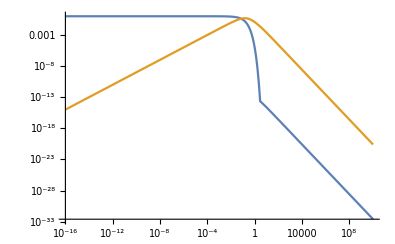

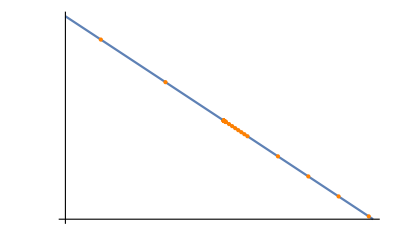

```mathematica
g0=10;
{rfi,rrad}=solEqs[g0,0,10^10,30,20];

dom=InterpolatingFunctionDomain[rrad]//Flatten;
InterpolatingFunctionCoordinates[rrad]⟦1⟧;
%⟦1;;10⟧
%%//Length

LogLogPlot[{rfi[x],rrad[x]},{x,10^-16,dom⟦2⟧}]

tab=Transpose[{InterpolatingFunctionCoordinates[rrad]//Flatten,InterpolatingFunctionValuesOnGrid[rrad]//Flatten}];
p1=ListLogLogPlot[tab,PlotRange->{{2.8,2.9},{0.02,0.025}},PlotStyle->Directive[Orange,PointSize[Large]]];
p2=LogLogPlot[{rrad[x]},{x,2.8,2.9}];
Show[p2,p1]

Clear[g0,dom,rfi,rrad,tab,p1,p2]
```

### Hubble H(x)

Computing the Hubble expansion rate as a function of time, assuming a certain Hubble scale H_scale.

```mathematica
Clear[HOfx]

HOfx[gg_?NumberQ,Hscale_,wx_:0,xLarge_:10^10,prec_:30,accu_:20]:=HOfx[gg,Hscale,wx,xLarge,prec,accu]=Block[{Hi=Hscale,wχ=wx,rχ,rr,xData,yData,Nsteps,data,Hfnx},

(*solving the reheating equations*)
{rχ,rr}=solEqs[gg,wx,xLarge,prec,accu];

(*getting the x-coordinates*)
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);
(*number of steps*)
Nsteps=(xData//Length)-1;
(*re-sampling x-coordinates logarithmically*)
xData={xData⟦1⟧}~Join~(10^Table[Log10[xData⟦2⟧]+(Log10[xData⟦-1⟧]-Log10[xData⟦2⟧])*((i-1)/(Nsteps-1)),{i,Nsteps}]);

(*getting the hubble parameter*)
yData=Table[hub[x],{x,xData}];
yData=Hi*yData;

(*building the dataset*)
data={xData,yData}//Transpose;
Hfnx=Interpolation[data];

Hfnx
]
```

#### Test

InterpolatingFunction[…]

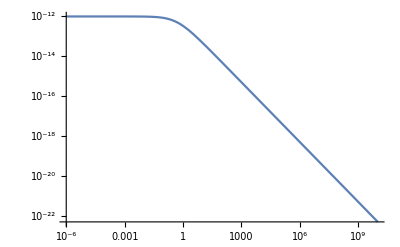

```mathematica
g0=30;
hf=HOfx[g0,10^-12,0,10^10,30,20]

dom=InterpolatingFunctionDomain[hf]//Flatten;

LogLogPlot[hf[x],{x,10^-6,dom⟦2⟧}]

Clear[g0,dom,hf]
```

### Temperature T(x)

Computing the temperature as a function of time, assuming a certain Hubble scale H_scale and a certain number of degrees of freedom g_*.

```mathematica
Clear[TOfx]

TOfx[gg_?NumberQ,gs_,Hscale_,wx_:0,xLarge_:10^10,prec_:30,accu_:20]:=TOfx[gg,gs,Hscale,wx,xLarge,prec,accu]=Block[{gstar=gs,Hi=Hscale,wχ=wx,rχ,rr,xData,yData,Nsteps,data,Tfnx},

(*solving the reheating equations*)
{rχ,rr}=solEqs[gg,wx,xLarge,prec,accu];

(*getting the x-coordinates*)
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);
(*number of steps*)
Nsteps=(xData//Length)-1;
(*re-sampling x-coordinates logarithmically*)
xData={xData⟦1⟧}~Join~(10^Table[Log10[xData⟦2⟧]+(Log10[xData⟦-1⟧]-Log10[xData⟦2⟧])*((i-1)/(Nsteps-1)),{i,Nsteps}]);

(*computing y-values*)
yData=rr[#]&/@xData;

(*getting the temperature*)
yData=((ρχi*yData)/Aρ)^(1/4);

(*building the dataset*)
data={xData,yData}//Transpose;
Tfnx=Interpolation[data];

Tfnx
]
```

#### Tests

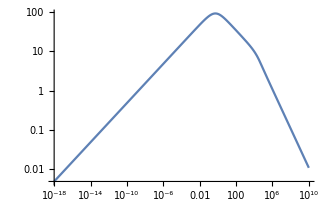

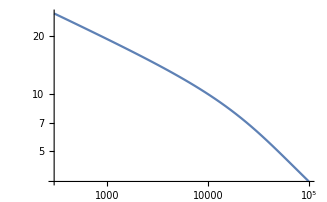

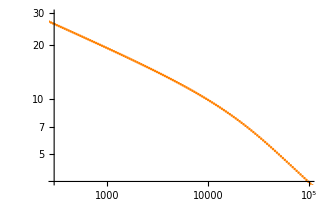

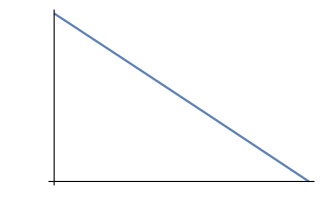

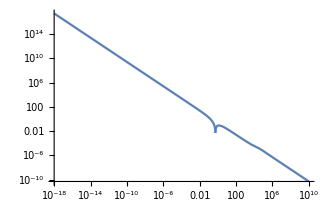

```mathematica
g0=0.0001;
(*{rfi,rrad}=solEqs[g0,0,10^10,30,20];
tab=Transpose[{InterpolatingFunctionCoordinates[rrad]//Flatten,InterpolatingFunctionValuesOnGrid[rrad]//Flatten}];
ListLogLogPlot[tab,PlotRange->{{300,100000},Automatic},PlotStyle->Directive[Orange(*,PointSize[Large]*)]]*)

tf=TOfx[g0,10,10^-12,0,10^10,30,20];
dom=InterpolatingFunctionDomain[tf]//Flatten;
tab=Transpose[{InterpolatingFunctionCoordinates[tf]//Flatten,InterpolatingFunctionValuesOnGrid[tf]//Flatten}];

LogLogPlot[tf[x],{x,10^-18,dom⟦2⟧}]
LogLogPlot[tf[x],{x,300,100000},PlotRange->All]
ListLogLogPlot[tab,PlotRange->{{300,100000},{3.5,30}},PlotStyle->Directive[Orange(*,PointSize[Large]*)]]
LogLogPlot[tf[x],{x,2.8,2.9},PlotRange->All]

dtf[x_]=D[Log[tf[x]],x];
LogLogPlot[{dtf[x]//Abs},{x,10^-18,dom[[2]]}(*,{x,0.01,1}*)(*,{x,300,100000}*)]

Clear[g0,rfi,rrad,tab,dom,tf,dtf]
```

### Scale factor

Computing the scale factor as a function of time.

```mathematica
Clear[aOfx]

aOfx[gg_?NumberQ,aini_:1,sum_:False,wx_:0,xLarge_:10^10,prec_:30,accu_:20]:=aOfx[gg,aini,sum,wx,xLarge,prec,accu]=Block[{wχ=wx,rχ,rr,domain,xData,efolds,yData,Nsteps,data,afnx},

(*solving the reheating equations*)
{rχ,rr}=solEqs[gg,wx,xLarge,prec,accu];

(*interpolation function properties*)
domain=(InterpolatingFunctionDomain[rr]//Flatten);

(*getting the x-coordinates*)
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);
(*number of steps*)
Nsteps=(xData//Length)-1;
(*re-sampling x-coordinates logarithmically*)
xData={xData⟦1⟧}~Join~(10^Table[Log10[xData⟦2⟧]+(Log10[xData⟦-1⟧]-Log10[xData⟦2⟧])*((i-1)/(Nsteps-1)),{i,Nsteps}]);

(*e-fold function*)
If[sum,
efolds[1]=0;
efolds[i_]:=efolds[i]=efolds[i-1]+((hub[xData⟦i⟧]+hub[xData⟦i-1⟧])/2)*(xData⟦i⟧-xData⟦i-1⟧),
efolds[1]=0;
efolds[i_]:=efolds[i]=efolds[i-1]+NIntegrate[hub[xx],{xx,xData⟦i-1⟧,xData⟦i⟧}]
];

(*computing e-folds*)
yData=Monitor[Table[efolds[i],{i,xData//Length}],ProgressIndicator[i,{1,xData//Length}]];
Clear[efolds];

(*computing scale factor*)
yData=aini*Exp[yData];

(*final data & interpolation*)
data={xData,yData}//Transpose;
afnx=Interpolation[data];

afnx
]
```

{24.6113,InterpolatingFunction[…]}

{0.102373,InterpolatingFunction[…]}

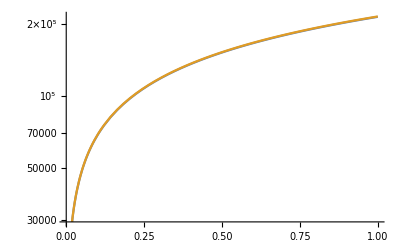

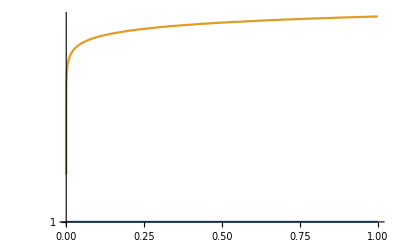

```mathematica
{time,afn1}=Timing[aOfx[0.1,1,False]]
dom=(InterpolatingFunctionDomain[afn1]//Flatten);
{time,afn2}=Timing[aOfx[0.1,1,True]]
LogPlot[{afn1[x],afn2[x]},{x,dom⟦1⟧,dom⟦2⟧}]
LogPlot[{1,afn2[x]/afn1[x]},{x,dom⟦1⟧,dom⟦2⟧}]

Clear[time,afn1,afn2,dom]
```

### Comoving time τ(x)

Computing the comoving time, with a given timescale t_scale:

τ(x)=t_scale((τ̄)_i+∫_x_i^x ⅆx'/(a(x'))).

```mathematica
Clear[tauOfx]

tauOfx[gg_?NumberQ,tscale_:1,aini_:1,sum_:False,wx_:0,xLarge_:10^10,prec_:30,accu_:20]:=tauOfx[gg,tscale,aini,sum,wx,xLarge,prec,accu]=Block[{wχ=wx,taui,ax,domain,xData,tau,yData,data,taufnx},

(*initial conformal time*)
taui=If[xd==0,0,taubarini[wχ]];

(*finding the scale factor a(x)*)
ax=aOfx[gg,aini,sum,wx,xLarge,prec,accu];

(*interpolation function properties*)
domain=(InterpolatingFunctionDomain[ax]//Flatten);
xData=(InterpolatingFunctionCoordinates[ax]//Flatten);

(*comoving time difference function*)
If[sum,
tau[1]=0;
tau[i_]:=tau[i]=tau[i-1]+((ax[xData⟦i⟧]^-1+ax[xData⟦i-1⟧]^-1)/2)*(xData⟦i⟧-xData⟦i-1⟧),
tau[1]=0;
tau[i_]:=tau[i]=tau[i-1]+NIntegrate[ax[xx]^-1,{xx,xData⟦i-1⟧,xData⟦i⟧}];
];

(*computing the comoving time difference*)
yData=Monitor[Table[tau[i],{i,xData//Length}],ProgressIndicator[i,{1,xData//Length}]];
Clear[tau];

(*adding initial comoving time and putting in the timescale*)
yData=tscale*(taui+yData);

(*final data & interpolation*)
data={xData,yData}//Transpose;

taufnx=Interpolation[data];

taufnx
]
```

{6.56431,InterpolatingFunction[…]}

{0.061131,InterpolatingFunction[…]}

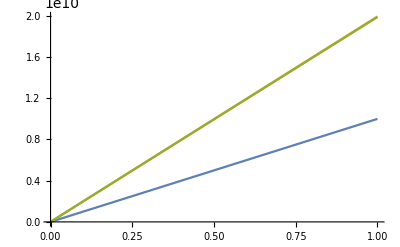

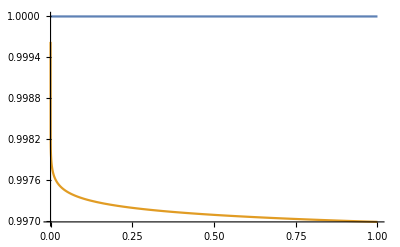

```mathematica
gam=0.1;
afn=aOfx[gam,1,False];

{time,tfn1}=Timing[tauOfx[gam,1,1,False]]
dom=(InterpolatingFunctionDomain[tfn1]//Flatten);
{time,tfn2}=Timing[tauOfx[gam,1,1,True]]

Plot[{x,afn[x]*tfn1[x],afn[x]*tfn2[x]},{x,dom⟦1⟧,dom⟦2⟧}]

Plot[{1,tfn2[x]/tfn1[x]},{x,dom⟦1⟧,dom⟦2⟧}]

Clear[gam,time,tfn1,tfn2,afn,dom]
```

### Redshift

We compute the total redshift (1+z) from today to the time when the GW were generated. For simplicity, it’s easier to start from the earliest times. We break the computation into three parts:
1. Redshift from GW generation until some time during the Dark Sector (DS) Radiation Domination (RD) era. Part of this process takes place during DS reheating (DSRH).
2. Redshift from this time until after the Visible Sector (VS) is reheated by the DS (VSRH).
3. Redshift from VSRH time until today.

For #1 the ratio (a(t_2))/(a(t_1))=(1+z_1)/(1+z_2) of scale factors between two times t_1<t_2 during DS reheating is simply equal to (a(t_2))/(a(t_1))=e^(∫_t_1^t_2 ⅆt  H(t))=e^(∫_x_1^x_2 ⅆx  h(x)).
For #2, VSRH can take place instantaneously or adiabatically. So we use either energy- or entropy-conservation as our guides.

```mathematica
Clear[redshift]

redshift[gg_?NumberQ,Hscale_,xRange_List,gUVs_List,IRs_List:{Automatic,0,gSM},instant_:True,wx_:0,xLarge_:10^10,prec_:30,accu_:20,debug_:False]:=redshift[gg,Hscale,xRange,gUVs,IRs,instant,wx,xLarge,prec,accu,debug]=Block[{Hi=Hscale,wχ=wx,xStar,xm,rχ,rr,efolds,Tdm,gdUV,gUV,gstar,gdIR,gd0,gIR,TIR=10^2,Gfactor,Z1,Z2,Z3,res},

(*the time-range between GW production (x_*) and an arbitrary point during DS-RD era (Subscript[x, m])*)
{xStar,xm}=xRange;

(*computing the efolds between x_* and Subscript[x, m]*)
{rχ,rr}=solEqs[gg,wx,xLarge,prec,accu];
efolds=NIntegrate[hub[x],{x,xStar,xm}];

(*the redshift factor between x_* and Subscript[x, m]*)
Z1=Exp[efolds];

(*total plasma UV d.o.f.: g_*^UV=Subscript[g, d]^UV+g^UV*)
{gdUV,gUV}=gUVs;
gstar=gdUV+gUV;

(*computing the plasma UV temperature at Subscript[x, m]*)
Tdm=TOfx[gg,gstar,Hscale,wx,xLarge,prec,accu][xm];

(*VSRH (IR) quantities: DS IR d.o.f., DS d.o.f. today, VS IR d.o.f.*)
{gdIR,gd0,gIR}=IRs;
gdIR=If[gdIR===Automatic,gdUV,gdIR];

(*computing the entropy dump from DS reheating the VS; whether instantaneously (for a non-equilibrium process, but energy-conserving and relativistic) or adiabatically (for an equilibrium process, entropy-conserving; e.g. freeze-out)*)
Gfactor=If[instant,(gstar/(gdIR+gIR))^(1/4),(gstar/(gdIR+gIR))^(1/3)];

(*the redshift factor between Subscript[x, m] and Subscript[x, IR], at some arbitrary time shortly after VS reheating*)
Z2=Gfactor*Tdm/TIR;

(*the redshift factor from the time of VS reheating down until today*)
Z3=((gIR+(gdIR-gd0))/gs0)^(1/3)*TIR/Tγ0;

(*the total redshift. Note that the explicit dependence on the VS temperature TIR after reheating from the DS cancels out; it only appears in gIR(TIR).*)
res=If[debug,{Z1*Z2*Z3,Z1,Z2,Z3},Z1*Z2*Z3];

res
]
```

#### Test

To double-check, we need to obtain the vanilla, traditional result. This is given by:

1. There is no DSRH (which can be mimicked by taking it to be extremely short).
2. There is actually no DS (which can be mimicked by taking T_d=T_SM and g_d=g_SM).

So to mimic this we search for a time at which T_d=100 GeV with g_d=100 (the benchmarks in the vanilla case). It doesn’t matter what Γ_d or H_d are, since we will take a vanishingly small redshift during DSRH.

For Γ=H_d=10*(1000 GeV)^2/m_Pl this time is x=150.783:

```mathematica
TOfx[1,100,10 1000^2/mpl][150.783]
```

100.001

We then compute the redshift from that time until today (note we take the xRange during DSRH to be vanishingly small). In terms of scale factor, we get a_*=8×10^-16, from the vanilla case.

```mathematica
redshift[1,10 1000^2/mpl,{150.783,150.783*(1+10^-6)},{0,100},{0,0,100}]
%^-1
```

1.22451×10^15

8.16653×10^-16

Splitting the result into its various parts:

```mathematica
redshift[1,10 1000^2/mpl,{150.783,150.783*(1+10^-6)},{0,100},{0,0,100},False,0,10^3,30,20,True]
redshift[1,10 1000^2/mpl,{150.783,150.783*(1+10^-6)},{0,100},{0,0,100},False,0,10^10,30,20,True]
```

{1.22451×10^15,1.,1.00001,1.22449×10^15}

{1.22451×10^15,1.,1.00001,1.22449×10^15}

### Crossings

```mathematica
Clear[xCross]

xCross[gg_?NumberQ,rCrit_,wx_:0,xLarge_:10^10,prec_:30,accu_:20]:=xCross[gg,rCrit,wx,xLarge,prec,accu]=Block[{wχ=wx,rχ,rr,xA,xB,xData,yData,xpk,xLSet,yLSet,xRSet,yRSet,xL0,xR0,xL,xR,eps=smallnum},

{rχ,rr}=solEqs[gg,wx,xLarge,prec,accu];
{xA,xB}=(InterpolatingFunctionDomain[rr]//Flatten);
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[rr]//Flatten);

(*slightly away from the leftmost edge*)
xA=If[xA<=0,Min[eps,xData⟦2⟧],Min[xData⟦2⟧,xA*(1+eps)]];

xpk=10^(LX/.FindMaximum[rr[10^LX]//Log10,{LX,0,Log10[xA],Log10[xB]},MaxIterations->10^6,WorkingPrecision->prec]⟦-1⟧);

(*the initial guesses for the Left/Right crossing times*)
xLSet=Select[xData,(#<xpk)&];
yLSet=yData⟦1;;Length@xLSet⟧;
yLSet=Abs[yLSet-rCrit];
xL0=(Position[yLSet,Min[yLSet]]//Flatten)⟦1⟧;
xL0=xLSet⟦xL0⟧;

xRSet=Select[xData,(#>xpk)&];
yRSet=yData⟦(Length@yData-Length@xRSet)+1;;-1⟧;
yRSet=Abs[yRSet-rCrit];
xR0=(Position[yRSet,Min[yRSet]]//Flatten)⟦1⟧;
xR0=xRSet⟦xR0⟧;
Clear[xLSet,xRSet,yLSet,yRSet,xData,yData];

xL=10^(LX/.FindRoot[Log10[rr[10^LX]]==Log10[rCrit],{LX,Log10[xL0],Log10[xA],Log10[xpk]},MaxIterations->10^6,WorkingPrecision->prec]//Quiet);
xR=10^(LX/.FindRoot[Log10[rr[10^LX]]==Log10[rCrit],{LX,Log10[xR0],Log10[xpk],Log10[xB]},MaxIterations->10^6,WorkingPrecision->prec]//Quiet);

{xL,xpk,xR}
]
```

### Find rate γ

```mathematica
Clear[gammaRate]

gammaRate[gg_?NumberQ,xCrit_,wx_:0,δ_:10^-6,xLarge_:10^10,prec_:30,accu_:20]:=gammaRate[gg,xCrit,wx,δ,xLarge,prec,accu]=Block[{rχ,rr,wχ=wx,γ},

{rχ,rr}=solEqs[gg,wx,xLarge,prec,accu];

γ=(xCrit-xd)/rr[xCrit]^(1/4)*(rr[(1+δ)xCrit]^(1/4)-rr[xCrit]^(1/4))/(δ xCrit);

γ
]
```

## Analytical Approximations

r_(r,c)≡r_r(x_c)=f^-4:

```mathematica
rrc=f^-4;
```

### Approximate Solutions & Useful Benchmarks

We take x_d=0.

#### χD: reheaton domination (r_r<<r_χ)

In the equation for r_χ we simply ignore r_r:

```mathematica
DSolve[{rχ'[x]+3 rχ[x]^(3/2)==-γ rχ[x],rχ[0]==1},rχ[x],x]//FullSimplify
rχSubSol={rχ[x]->γ^2/((-3+ⅇ^((x γ)/2) (3+γ))^2)}(*the non-singular solution, simplified*);
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rχ[x]→γ^2/((-3+ⅇ^((x γ)/2) Abs[-3+γ])^2)},{rχ[x]→γ^2/((3+ⅇ^((x γ)/2) Abs[-3+γ])^2)},{rχ[x]→γ^2/((-3+ⅇ^((x γ)/2) (3+γ))^2)},{rχ[x]→γ^2/((3+ⅇ^((x γ)/2) (3+γ))^2)}}

```mathematica
(*{rχ[x]->(ⅇ^(-(-2/3+x) γ) γ^2)/((-3+3 ⅇ^(-1/2 (-2/3+x) γ)-γ)^2),rr[x]->1/20 ⅇ^(-11 γ/9) γ^2 (-(ⅇ^(1/3 (1+4 x) γ) γ^(5/3) (8+γ))/((-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(8/3))+(5 ⅇ^(11 γ/9))/(-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))+(ⅇ^((8 γ)/9+(x γ)/2) (3+γ))/(-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ)))};

((rr[x]/.%)/.(x->x+2/3))//Simplify//Expand

(Total@(FullSimplify/@(Expand/@(List@@%))))
%//FullSimplify
(%%/.x->0)//Simplify*)
```

Substituting into the equation for r_r:

```mathematica
Assuming[γ>0&&x>0,({rr'[x]+4 rχ[x]^(1/2)rr[x]==γ rχ[x],rr[0]==0}/.rχSubSol)//FullSimplify]
Assuming[γ>0&&x>0,DSolve[%,rr[x],x]//Simplify]//Flatten
rrSubSol={rr[x]->Assuming[γ>0&&x>0,((γ^2 (-ⅇ^((4 x γ)/3) γ^(5/3) (8+γ)-15 (-3+ⅇ^((x γ)/2) (3+γ))^(2/3)+2 ⅇ^((x γ)/2) (3+γ) (-3+ⅇ^((x γ)/2) (3+γ))^(2/3)+ⅇ^(x γ) (3+γ)^2 (-3+ⅇ^((x γ)/2) (3+γ))^(2/3)))/(20 (-3+ⅇ^((x γ)/2) (3+γ))^(8/3)))//FullSimplify]}(*the real-valued solution *);
(*testing:*)
%%/.{γ->10,x->0}
rrSubSol/.{γ->10,x->0}
```

{(-3+ⅇ^((x γ)/2) (3+γ)) (4 γ rr[x]+(-3+ⅇ^((x γ)/2) (3+γ)) rr'[x])==γ^3,rr[0]==0}

{rr[x]→-((-1)^(1/3) γ^2 (ⅇ^((4 x γ)/3) (-γ)^(5/3) (8+γ)-15 (3-ⅇ^((x γ)/2) (3+γ))^(2/3)+2 ⅇ^((x γ)/2) (3+γ) (3-ⅇ^((x γ)/2) (3+γ))^(2/3)+ⅇ^(x γ) (3+γ)^2 (3-ⅇ^((x γ)/2) (3+γ))^(2/3)))/(20 (-3+ⅇ^((x γ)/2) (3+γ))^(8/3))}

{rr[0]→0}

{rr[0]→0}

Putting them together: the solution rules, for r_χ>>r_r:

```mathematica
SubSol=rχSubSol~Join~rrSubSol
```

{rχ[x]→γ^2/((-3+ⅇ^((x γ)/2) (3+γ))^2),rr[x]→(γ^2 (-ⅇ^((4 x γ)/3) γ^(5/3) (8+γ)-15 (-3+ⅇ^((x γ)/2) (3+γ))^(2/3)+2 ⅇ^((x γ)/2) (3+γ) (-3+ⅇ^((x γ)/2) (3+γ))^(2/3)+ⅇ^(x γ) (3+γ)^2 (-3+ⅇ^((x γ)/2) (3+γ))^(2/3)))/(20 (-3+ⅇ^((x γ)/2) (3+γ))^(8/3))}

These expressions are too complicated. It is convenient to split them into two cased depending on whether γ>>1 or γ<<1

```mathematica
Normal@Series[{rχ[x],rr[x]}/.SubSol,{x,0,1}];
solsAn["γ>>1","χD"]={rχ[x]->(%⟦1⟧)//FullSimplify,rr[x]->%⟦2⟧//FullSimplify}

Normal@Series[{rχ[x],rr[x]}/.SubSol,{γ,0,1}];
solsAn["γ<<1","χD"]={rχ[x]->(%⟦1⟧)//FullSimplify,rr[x]->(%⟦2⟧)//FullSimplify}
```

{rχ[x]→1-x (3+γ),rr[x]→x γ}

{rχ[x]→(8-2 x (-6+(4+3 x) γ))/(2+3 x)^3,rr[x]→4/5 (-(2 2^(2/3))/(2+3 x)^(8/3)+1/(2+3 x)) γ}

#### χR equality: r_eq≡r_r(x_eq)=r_χ(x_eq)

For the γ>>1 case they become equal shortly after the decays start

```mathematica
{rχ[x],rr[x]}/.solsAn["γ>>1","χD"];
Solve[%⟦1⟧==%⟦2⟧,x]//Flatten
(%%/.%)⟦1⟧//Simplify
xEq["γ>>1"]=Normal@Series[x/.%%,{γ,∞,1}]
rEq["γ>>1"]=Normal@Series[%%,{γ,∞,1}]
```

{x→1/(3+2 γ)}

γ/(3+2 γ)

1/(2 γ)

1/2-3/(4 γ)

For the γ<<1 case this happens much later

```mathematica
Normal@Series[({rχ[x],rr[x]}/.solsAn["γ<<1","χD"])/.x->1/t,{t,0,2}]/.t->1/x
x/.Assuming[0<γ<1,Solve[%⟦1⟧==%⟦2⟧,x,Reals]//Flatten]//FullSimplify
(*xEq["γ<<1"]=Normal@Series[%,{γ,0,-1}]*)
xEq["γ<<1"]=%
(%%%/.{x->%%})⟦1⟧//FullSimplify
(*rEq["γ<<1"]=Normal@Series[%,{γ,0,2}]*)
rEq["γ<<1"]=%
```

{-(2 γ)/(9 x)+(4 (3+γ))/(27 x^2),-(8 γ)/(45 x^2)+(4 γ)/(15 x)}

2/3+10/(11 γ)

2/3+10/(11 γ)

(66 γ^2)/(15+11 γ)^2

(66 γ^2)/(15+11 γ)^2

#### RD: radiation domination (r_r>>r_χ)

Computing r_χ(x) in the r_r>>r_χ & γ>>1 limits

```mathematica
Assuming[γ>1&&x>0,DSolve[{rχ'[x]==-γ rχ[x],rχ[xEq["γ>>1"]]==rEq["γ>>1"]},rχ[x],x]//Simplify]//Flatten
(rχ[x]/.%)
rχSupSol={rχ[x]->%}
```

{rχ[x]→(ⅇ^(1/2-x γ) (-3+2 γ))/(4 γ)}

(ⅇ^(1/2-x γ) (-3+2 γ))/(4 γ)

{rχ[x]→(ⅇ^(1/2-x γ) (-3+2 γ))/(4 γ)}

Defining r_t≡r_χ+r_r, and substituting γ r_χ=-r_χ' into the equation for r_r':

r_t'(x)+4 r_t^(3/2)-4 r_t^(1/2)r_χ=0

Further defining y≡r_t^(1/2):
y'+2 y^2=2 r_χ=p^2 e^(-γ x);    with   p≡e^(1/4)·((-3+2γ)/(4γ))^(1/2).

```mathematica
(Assuming[γ>1&&x>0&&p>0,DSolve[{y'[x]+2 y[x]^2==p^2 Exp[-γ*x],y[xEq["γ>>1"]]==(2rEq["γ>>1"])^(1/2)},y[x],x]//Expand]//Flatten)/.p->((-3+2γ)/(4γ))^(1/2)*E^(1/4);
Assuming[k>0&&t>0&&x>0,(((y[x]/.%)/.γ->1/t))//FullSimplify]
temp=Assuming[k>0&&t>0&&x>0,Normal@Series[%,{t,0,1}]//FullSimplify]
```

-((ⅇ^(1/4-x/(2 t)) (-2+3 t) (BesselI[1,ⅇ^(1/4-x/(2 t)) √(4-6 t) t] (2 BesselK[0,√(4-6 t) t]-BesselK[1,√(4-6 t) t])+(2 BesselI[0,√(4-6 t) t]+BesselI[1,√(4-6 t) t]) BesselK[1,ⅇ^(1/4-x/(2 t)) √(4-6 t) t]))/(2 √(4-6 t) ((2 BesselI[0,√(4-6 t) t]+BesselI[1,√(4-6 t) t]) BesselK[0,ⅇ^(1/4-x/(2 t)) √(4-6 t) t]+(-2 BesselK[0,√(4-6 t) t]+BesselK[1,√(4-6 t) t]) Hypergeometric0F1Regularized[1,1/4 ⅇ^(1/2-x/t) (4-6 t) t^2])))

((-4+3 t) (-ⅇ^(x/t) (4+5 t)+√ⅇ t (2+4 x-t (-2+8 EulerGamma+x)-8 t Log[t])))/(32 √ⅇ t^2 x+4 ⅇ^(x/t) (4-t+4 (2+t) x))

```mathematica
Normal@Series[Numerator[#]&@temp,{t,0,1}]
Normal@Series[Denominator[#]&@temp,{t,0,1}]
Normal@Series[(%%/%)//Simplify,{t,0,0}]/.t->1/γ

rrSupSol={rr[x]->(%^2-0rχ[x]/.rχSupSol)//FullSimplify}
```

ⅇ^(x/t) (16+8 t)-8 √ⅇ t (1+2 x)

ⅇ^(x/t) (4 t (-1+4 x)+4 (4+8 x))

1/(1+2 x)

{rr[x]→1/(1+2 x)^2}

The solution rules, for r_r>>r_χ and γ>>1

```mathematica
solsAn["γ>>1","RD"]=rχSupSol~Join~rrSupSol
Clear[temp]
```

{rχ[x]→(ⅇ^(1/2-x γ) (-3+2 γ))/(4 γ),rr[x]→1/(1+2 x)^2}

Now for the γ<<1 limit

```mathematica
Assuming[γ>1&&x>0&&p>0,DSolve[{rr'[x]+4 rr[x]^(3/2)==0,rr[xEq["γ<<1"]]==rEq["γ<<1"]},rr[x],x]⟦2⟧]//Flatten//FullSimplify
Assuming[γ>1&&x>0&&p>0,DSolve[{rχ'[x]+3(rr[x]/.%)^(1/2)rχ[x]==-γ rχ[x],rχ[xEq["γ<<1"]]==rEq["γ<<1"]},rχ[x],x]]//Flatten//FullSimplify
Normal@Series[rr[x]/.%%,{x,∞,2}];
Normal@Series[rχ[x]/.%%,{x,∞,2}]//Simplify;
solsAn["γ<<1","RD"]={rχ[x]->%,rr[x]->%%}
```

{rr[x]→(4356 γ^2)/(132 x γ+(-8+√66) (15+11 γ))^2}

{rχ[x]→(66 66^(3/4) ⅇ^(10/11+(2 γ)/3-x γ) γ^2)/(√(15+11 γ) (132 x γ+(-8+√66) (15+11 γ))^(3/2))}

{rχ[x]→1/2 (33/2)^(1/4) ⅇ^(10/11+(2 γ)/3-x γ) √(γ/(x^3 (15+11 γ))),rr[x]→1/(4 x^2)}

#### L_r≡1/4(d ln r_r)/(d x)=(d ln T)/(d x)

Computing L_r≡1/4(d ln r_r)/(d x):

```mathematica
Do[Do[Lr[γRegime,era]=1/4 D[Log[rr[x]/.solsAn[γRegime,era]],x]//Expand//Simplify//FullSimplify,{γRegime,{"γ<<1","γ>>1"}}],{era,{"χD","RD"}}]
```

A simplified version for the case γ<<1, χD:

```mathematica
simple=(-2/(2+3 x)+5/(4 (2+3 x-(2 2^(2/3))/(2+3 x)^(2/3))));
(simple/Lr["γ<<1","χD"])//Simplify

Lr["γ<<1","χD"]=simple;

Clear[simple]
```

1

```mathematica
?Lr
```

#### Maximum: r_(r,max)≡r_r(x_max)

For γ<<1 it occurs during χD:

```mathematica
xMax["γ<<1"]=(x/.(Solve[Lr["γ<<1","χD"]==0,x]//Flatten))
(*%/(2/3(8/3)^(3/5))*)
rrMax["γ<<1"]=((rr[x]/.solsAn["γ<<1","χD"])/.x->xMax["γ<<1"])//FullSimplify
%/(2/3(3/8)^(8/5)γ)

xMax["γ<<1"]=xMax["γ<<1"]//N
```

Root0.534Root[-15520+6480 #1+19440 #1^2+29160 #1^3+21870 #1^4+6561 #1^5&,1]0.5341867009072119

(3^(3/5) γ)/(8 2^(4/5))

1

0.534187

```mathematica
(3^(3/5) γ)/(8 2^(4/5))//N
%^(1/4)
```

0.13879 γ

0.610365 γ^(1/4)

For γ>>1 it occurs somewhere between χD & RD, so we need to combine both regimes

```mathematica
combined=(1/(rr[x]/.solsAn["γ>>1","χD"])+1/(rr[x]/.solsAn["γ>>1","RD"]))^-1;
1/4 D[Log[combined],x]//Simplify

Numerator[%];
(x/.#&)/@Solve[%==0,x];
(Normal@Series[#,{γ,∞,1}]&/@%)//FullSimplify//Expand

(*selecting the only solution with x>2/3, as is necessary*)
Normal@Series[%,{γ,1,1}](*it's enough to expand γ above 1 to check this out*);
Assuming[γ>1,Select[%,#>0&]]⟦1⟧(*the result must be larger than 2/3*);
Position[%%,%](*selecting the correct element from the list*);

xMax["γ>>1"]=(%%%%⟦(%//Flatten)⟦1⟧⟧)(*the full x solution*)
rrMax["γ>>1"]=Normal@Series[(combined/.{x->xMax["γ>>1"]})//FullSimplify,{γ,∞,1}]

Clear[combined]
```

(1-4 x^2 γ-8 x^3 γ)/(4 x+4 x^2 γ+16 x^3 γ+16 x^4 γ)

{-1/2+1/(2 γ),-1/(4 γ)+1/(2 √γ),-1/(4 γ)-1/(2 √γ)}

-1/(4 γ)+1/(2 √γ)

1+15/γ-4/(√γ)

#### L_(r,max)^(2)≡(d^2 lnT)/(d x^2)|_max

We are also interested in the second derivative of lnT w.r.t. x, at the location of the maximum. We will take advantage of the fact that 

(d lnT)/(d x)|_max=1/4(d ln r_r)/(d x)|_max=1/4(γ r_χ/r_r-4h)=0

and, of course, r_r'=0 too.

Indeed:

(d^2 ln r_r)/(d x^2)=d/dx(γ r_χ/r_r-4h)=(d ln r_χ)/(d x)(4h-(2 r_χ)/h)=-(γ+3h)(4h-(2 r_χ)/h).

We have found that x_max occurs during RD for γ>>1, and during χD for γ<<1.

```mathematica
xMax["γ>>1"]
xEq["γ>>1"]
Simplify[%%>%]

xMax["γ<<1"]
xEq["γ<<1"]
Simplify[%%<%]
```

-1/(4 γ)+1/(2 √γ)

1/(2 γ)

2 √γ>3

0.534187

2/3+10/(11 γ)

True

So h(x_max)≈1 for γ>>1 (RD):

√(1/(1+2 x)^2+(ⅇ^(1/2-x γ) (-3+2 γ))/(4 γ))

√((ⅇ^(3/4-(√γ)/2) (-3+2 γ))/(4 γ)+(4 γ^2)/(1-2 (√γ+γ))^2)

√(1+ⅇ^(3/4-(√γ)/2) (1/2-3/(4 γ))+47/(4 γ^2)-7/γ^(3/2)+4/γ-2/(√γ))

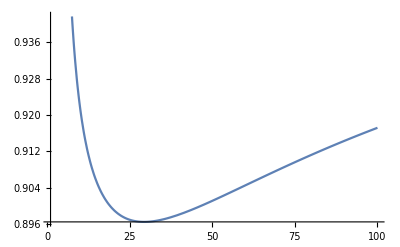

```mathematica
(rχ[x]+rr[x])^(1/2)/.solsAn["γ>>1","RD"]
(%/.x->xMax["γ>>1"])//FullSimplify
Normal@Series[%,{γ,∞,2}]
Plot[%,{γ,1,100}]
```

So finally:

(d^2 lnT)/(d x^2)=1/4(d^2 ln r_r)/(d x^2)≈-γ h_max≈-γ

```mathematica
L2rrMax["γ>>1"]=-γ*1;
```

While for γ<<1 (χD) we have h(x_max)≈√(r_χ(x_max))≈0.56 (r_χ(x_max)≈0.31)

```mathematica
(rχ[x]+rr[x])^(1/2)/.solsAn["γ<<1","χD"]
(%/.x->xMax["γ<<1"])//FullSimplify
Normal@Series[%,{γ,0,1}]
```

√(4/5 (-(2 2^(2/3))/(2+3 x)^(8/3)+1/(2+3 x)) γ+(8-2 x (-6+(4+3 x) γ))/(2+3 x)^3)

√(0.308203+0.0107708 γ)

0.555161+0.00970058 γ

```mathematica
(rχ[x])/.solsAn["γ<<1","χD"]
(%/.x->xMax["γ<<1"])//FullSimplify
```

(8-2 x (-6+(4+3 x) γ))/(2+3 x)^3

0.308203-0.128019 γ

So finally:

(d^2 lnT)/(d x^2)=1/4(d^2 ln r_r)/(d x^2)≈-(3h)/4(4h-(2 r_χ)/h)

```mathematica
L2rrMax["γ<<1"]=-3/4 0.55516075873073(4*0.55516075873073-(2*0.30820346803447984)/0.55516075873073);
```

### Reheating quantities at critical temperature

#### r_(r,c)≡r_r(x_c)

Now we search for x_c & r_(r,c). There’s always two solutions for x_c. Also, it is important to keep in mind that we will assume r_(r,c) is close to r_(r,max), which translates into a condition for the smallest allowed f: f_min(γ)

```mathematica
Solve[rrMax["γ<<1"]==rrc,f]
%//N
Solve[rrMax["γ>>1"]==rrc,f]
%//N
```

{{f→-2^(19/20)/(3^(3/20) γ^(1/4))},{f→-(ⅈ 2^(19/20))/(3^(3/20) γ^(1/4))},{f→(ⅈ 2^(19/20))/(3^(3/20) γ^(1/4))},{f→2^(19/20)/(3^(3/20) γ^(1/4))}}

{{f→-1.63836/γ^(1/4)},{f→-(0.+1.63836 ⅈ)/γ^(1/4)},{f→(0.+1.63836 ⅈ)/γ^(1/4)},{f→1.63836/γ^(1/4)}}

{{f→-γ^(1/4)/(15-4 √γ+γ)^(1/4)},{f→-(ⅈ γ^(1/4))/(15-4 √γ+γ)^(1/4)},{f→(ⅈ γ^(1/4))/(15-4 √γ+γ)^(1/4)},{f→γ^(1/4)/(15-4 √γ+γ)^(1/4)}}

{{f→-(1. γ^(1/4))/(15.-4. √γ+γ)^(1/4)},{f→-((0.+1. ⅈ) γ^(1/4))/(15.-4. √γ+γ)^(1/4)},{f→((0.+1. ⅈ) γ^(1/4))/(15.-4. √γ+γ)^(1/4)},{f→γ^(1/4)/(15.-4. √γ+γ)^(1/4)}}

Now let us find x_c1 & x_c2.

For γ<<1, x_c1 occurs during χD, while x_c2 can be either. Since 0<x_c1<x_max≈1 then the first one lies somewhere after 0, whereas the other one lies when x>1.

```mathematica
?solsAn
```

```mathematica
xc1=(x/.Solve[Normal@Series[((rr[x]/.solsAn["γ<<1","χD"])),{x,0,1}]==rrc,x]//FullSimplify//Flatten)⟦1⟧;
xc2=Min[(x/.Solve[Normal@Series[((rr[x]/.solsAn["γ<<1","χD"])),{x,∞,1}]==rrc,x]//FullSimplify//Flatten)⟦1⟧,x/.Solve[((rr[x]/.solsAn["γ<<1","RD"]))==rrc,x]⟦2⟧];

xcVals["γ<<1"]={xc1,xc2}

Clear[xc1,xc2]
```

{1/(f^4 γ),Min[f^2/2,(4 f^4 γ)/15]}

For γ>>1 x_c1 occurs during χD, whereas x_c2 during RD

```mathematica
xc1=(x/.Solve[(rr[x]/.solsAn["γ>>1","χD"])==rrc,x]//FullSimplify//Flatten)⟦1⟧

(*(*w/o expanding for large x*)
(x/.Solve[(rr[x]/.solsAn["γ>>1","RD"])==rrc,x]//FullSimplify//Flatten)(*two solutions, need to pick up the positive one*)*)

(*expanding for large x*)
(x/.Solve[Normal@Series[(rr[x]/.solsAn["γ>>1","RD"]),{x,∞,2}]==rrc,x]//FullSimplify//Flatten)(*two solutions, need to pick up the positive one*)

Select[(%/.f->2),#>0&]⟦1⟧(*it's enough to check for a specific value of f, say f=2*);
Position[(%%/.f->2),%](*selecting the correct element from the list*);
xc2=(%%%⟦(%//Flatten)⟦1⟧⟧)(*the full xc2 solution*);

xcVals["γ>>1"]={xc1,xc2}

Clear[xc1,xc2]
```

1/(f^4 γ)

{-f^2/2,f^2/2}

{1/(f^4 γ),f^2/2}

#### L_(r,c)≡L_r(x_c)=1/4((d ln r_r)/(d x))_x_c

```mathematica
xcVals["γ<<1"]
(*for Subscript[x, c1]: χD*)
tmp1=Normal@Series[(Lr["γ<<1","χD"]/.x->xcVals["γ<<1"]⟦1⟧)/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ

(*for Subscript[x, c2]: χD or RD*)
tmp2=Normal@Series[(Lr["γ<<1","χD"]/.x->(4 f^4 γ)/15)/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ
tmp3=(Normal@Series[(Lr["γ<<1","RD"]/.x->f^2/2)/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ)//FullSimplify

LrcVals["γ<<1"]={tmp1,If[((4 f^4 γ)/15==xcVals["γ<<1"]⟦2⟧)//Simplify,-15/(16 f^4 γ),-1/f^2]}

Clear[tmp1,tmp2,tmp3]
```

{1/(f^4 γ),Min[f^2/2,(4 f^4 γ)/15]}

-7/8+67/(48 f^4 γ)+(f^4 γ)/4

-15/(16 f^4 γ)

-1/f^2

{-7/8+67/(48 f^4 γ)+(f^4 γ)/4,If[8 f^2 γ≤15,-15/(16 f^4 γ),-1/f^2]}

```mathematica
xcVals["γ>>1"]
(*(*w/o expanding for large x*)
LrcVals["γ>>1"]={(Normal@Series[(Lr["γ>>1","χD"]/.x->xcVals["γ>>1"]⟦1⟧)/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ),Lr["γ>>1","RD"]/.x->xcVals["γ>>1"]⟦2⟧}*)

(*expanding for large x*)
LrcVals["γ>>1"]={(Normal@Series[(Lr["γ>>1","χD"]/.x->xcVals["γ>>1"]⟦1⟧)/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ),Normal@Series[Lr["γ>>1","RD"],{x,∞,1}]/.x->xcVals["γ>>1"]⟦2⟧}
```

{1/(f^4 γ),f^2/2}

{(f^4 γ)/4,-1/f^2}

#### H_c≡H(x_c)=H_dec √(r_χ+r_r)

For γ<<1, x_c1 occurs during χD, while x_c2 could be either.

```mathematica
(rχ[x]/.solsAn["γ<<1","χD"])
xcVals["γ<<1"]
```

(8-2 x (-6+(4+3 x) γ))/(2+3 x)^3

{1/(f^4 γ),Min[f^2/2,(4 f^4 γ)/15]}

For x_c1≈0, we find r_(χ,c1)≈1

```mathematica
(rχ[x]/.solsAn["γ<<1","χD"]);
Normal@Series[%,{x,0,1}](*for Subscript[x, c1]≈0*);
%/.x->xcVals["γ<<1"]⟦1⟧
```

1+(-3-γ)/(f^4 γ)

For x_c2 during χD, we find that the dominant term goes like r_(χ,c2)≈(5/2 1/(f^4 γ))^2:

```mathematica
(*Total[FullSimplify/@(List@@(((rχ[x]/.solsAn["γ<<1","χD"])/.x->xcVals["γ<<1"]⟦2⟧)//Expand))]*)
Total[FullSimplify/@(List@@((((rχ[x]+rr[x])/.solsAn["γ<<1","χD"])/.x->(4 f^4 γ)/15)//FullSimplify//Expand))]

(*check*)
g0=0.01;
%%/.{γ->g0};
{(7.2/g0)^(1/4),(3.3/g0^2)^(1/4)}
(%%/.f->#)&/@%

((50 f^4 γ)/((5+2 f^4 γ)^3)/.{γ->g0,f->#})&/@%%
Clear[g0]
```

125/((5+2 f^4 γ)^3)+(50 γ)/((5+2 f^4 γ)^3)+(50 f^4 γ)/((5+2 f^4 γ)^3)+(20 f^4 γ^2)/(3 (5+2 f^4 γ)^3)+(4 f^8 γ^3)/(3 (5+2 f^4 γ)^3)-(10 5^(2/3) γ)/((5+2 f^4 γ)^(8/3))

{5.18004,13.4781}

{0.066547,0.0000615376}

{0.0493057,0.0000561073}

For x_c2 during RD, r_tot≈r_r(x_c2)=r_(r,c):

```mathematica
(((rr[x])/.solsAn["γ<<1","RD"])/.x->f^2/2)//FullSimplify
```

1/f^4

For γ>>1 x_c1 occurs during χD, x_c2 during RD

```mathematica
xcVals["γ>>1"]
(rχ[x]/.solsAn["γ>>1","χD"])/.{x->%⟦1⟧}
Normal@Series[(rr[x]/.solsAn["γ>>1","RD"]),{x,∞,2}]/.{x->%%⟦2⟧}
```

{1/(f^4 γ),f^2/2}

1-(3+γ)/(f^4 γ)

1/f^4

So putting everything together:

```mathematica
HdecFactor=Assuming[Arho>0&&mPL>0,√(f^4 Arho/3 Tc^4/mPL^2)//Simplify];
HcVals["γ<<1"]=(HdecFactor*{√1,If[(4 f^4 γ)/15==xcVals["γ<<1"]⟦2⟧,√((50 f^4 γ)/((5+2 f^4 γ)^3)),√(f^-4)//Simplify]})//Simplify
HcVals["γ>>1"]=(HdecFactor*{√1,√(f^-4)//Simplify})//Simplify
```

{(√((Arho f^4 Tc^4)/mPL^2))/(√3),Piecewise[{{(√(Arho Tc^4))/(√3 mPL), 8 f^2 γ>15}, {5 √(2/3) √((Arho f^8 Tc^4 γ)/(mPL^2 (5+2 f^4 γ)^3)), True}}]}

{(√((Arho f^4 Tc^4)/mPL^2))/(√3),(√(Arho Tc^4))/(√3 mPL)}

#### (a(x_c2))/(a(x_c1))

We are searching for the relative scale factor between x_c1 and x_c2. For that, we need to find a(x):

```mathematica
(xOfa[w,a]-xOfa[w,1])//FullSimplify
aΔx=(a/.Solve[Δx==%,a]⟦1⟧)//FullSimplify
```

(2 (-1+a^((3 (1+w))/2)))/(3 (1+w))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(1+3/2 (1+w) Δx)^(2/(3 (1+w)))

For γ>>1 x_c1<<1 is in χD and x_c2 is in RD. The Universe reheats very quickly, and so we can simply read the relative scale factor as T_max/T_c

```mathematica
(rrMax["γ>>1"]/rrc)^(1/4)
(Normal@Series[%,{γ,∞,0}])
```

(f^4 (1+15/γ-4/(√γ)))^(1/4)

f

For γ<<1, at x_c1<<1 we always have χD, and a(x_c1)≈1:

```mathematica
Normal@Series[aΔx/.w->0,{Δx,0,1}]
```

1+Δx

If x_c2<x_eq the relative scale factor is simply given by that in χD as well

```mathematica
(aΔx/.w->0)/.Δx->(4 f^4 γ)/15
```

(1+(2 f^4 γ)/5)^(2/3)

If x_c2>x_eq then we compute the scale factor up to x_eq, and then multiply by T_eq/T_c

```mathematica
fac1=((aΔx/.w->0)/.Δx->xEq["γ<<1"])//FullSimplify
```

(2+15/(11 γ))^(2/3)

```mathematica
rEq["γ<<1"]/rrc
Normal@Series[%,{γ,0,2}]
fac2=(%^(1/4))//FullSimplify
```

(66 f^4 γ^2)/(15+11 γ)^2

(22 f^4 γ^2)/75

((22/3)^(1/4) f √γ)/(√5)

Putting everything together

```mathematica
(fac1*fac2)//FullSimplify
Normal@Series[%,{γ,0,0}]
%//N
```

((22/3)^(1/4) f (2+15/(11 γ))^(2/3) √γ)/(√5)

(2^(1/4) 3^(5/12) 5^(1/6) f)/(11^(5/12) γ^(1/6))

(0.904981 f)/γ^(1/6)

```mathematica
acRel["γ<<1"]=If[((4 f^4 γ)/15==xcVals["γ<<1"]⟦2⟧)//FullSimplify,(1+(2 f^4 γ)/5)^(2/3),(0.9049808797604288 f)/γ^(1/6)];
acRel["γ>>1"]=f;
```

### Recap

```mathematica
?solsAn
```

```mathematica
?Lr
```

```mathematica
?xEq
```

```mathematica
?rEq
```

```mathematica
?xMax
```

```mathematica
?rrMax
```

```mathematica
?xcVals
```

```mathematica
?LrcVals
```

```mathematica
?HcVals
```

```mathematica
?acRel
```

## Examples

Exact {x_c1,x_max,x_c2}:

{0.0066094048662048051042907294794,0.14817230375348349995526154433,1.52605460074266389618790511369}

Approximate {x_c1,x_max,x_c2}:

{0.00625,0.133114,2.}

Error [(Approx-Exact)/Exact]:

{-0.0543778,-0.101628,0.310569}

γ_c^RATE

{0.2360888572610705113283,-0.38151182980932939491968}

Exact L_(r, c1):35.7198, Approximate L_(r, c1):40

Exact L_(r, c2):-0.249999, Approximate L_(r, c2):-1/4

Exact L_(r, max)^(2):-8.67698, Approximate L_(r, max)^(2):-10

-Graphics-

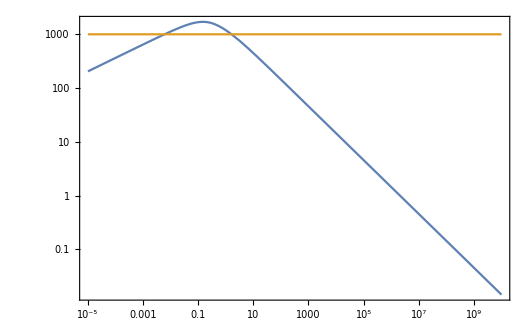

```mathematica
wχ=0;
gam=10;
regime=If[gam≤1,"γ<<1","γ>>1"];

eff=Max[2/gam^(1/4),2];
rcrit=eff^-4;

res=solEqs[gam];
Print["Exact {x_c1,x_max,x_c2}:"]
xLR=xCross[gam,rcrit]
(xcVals[regime]/.{γ->gam,f->eff})//N;
(xMax[regime]/.{γ->gam,f->eff})//N;
Print["Approximate {x_c1,x_max,x_c2}:"]
{%%%⟦1⟧,%%,%%%⟦2⟧}
Print["Error [(Approx-Exact)/Exact]:"]
(%%/%%%%%%)-1

domain=InterpolatingFunctionDomain[res⟦2⟧]//Flatten;

Print["γ_c^RATE"]
{gammaRate[gam,xLR⟦1⟧],gammaRate[gam,xLR⟦-1⟧]}

Print["Exact L_(r, c1):",D[Log[TOfx[gam,gSS,HI][x]],x]/.x->xLR⟦1⟧,", Approximate L_(r, c1):",LrcVals[regime]⟦1⟧/.{f->eff,γ->gam}]

Print["Exact L_(r, c2):",D[Log[TOfx[gam,gSS,HI][x]],x]/.x->xLR⟦3⟧,", Approximate L_(r, c2):",LrcVals[regime]⟦2⟧/.{f->eff,γ->gam}]

Print["Exact L_(r, max)^(2):",D[Log[TOfx[gam,gSS,HI][x]],{x,2}]/.x->xLR⟦2⟧,", Approximate L_(r, max)^(2):",L2rrMax[regime]/.γ->gam];

p1=LogLogPlot[{res⟦1⟧[xd+dx],res⟦2⟧[xd+dx]},{dx,10^-5,domain⟦2⟧-xd},PlotRange->{10^-8,100},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->{(xLR-xd)~Join~{1/gam},{rcrit}},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_{\\chi}",Magnification->1.7],MaTeX["\\rho_{r}",Magnification->1.7]}],{0.9,0.85}],Epilog->{Inset[Rotate[MaTeX["\\color{black} t=t_\\textrm{max}",Magnification->1.5],90°],Scaled[{.43,.2}]],Inset[Rotate[MaTeX["\\color{black} t=\\Gamma_\\chi^{-1}",Magnification->1.5],90°],Scaled[{.63,.2}]],Inset[Rotate[MaTeX["\\color{black} T=T_c",Magnification->1.5],0°],Scaled[{.08,.55}]],Inset[Rotate[MaTeX[ToString["\\begin{aligned} \\Gamma_\\chi &= "<>ToString[gam]<>"H_i \\end{aligned}"],Magnification->1.3],0°],Scaled[{.13,.9}]]}];

χDFns={rχ[x]/.solsAn[regime,"χD"],rr[x]/.solsAn[regime,"χD"]}/.{γ->gam,f->eff};
RDFns={rχ[x]/.solsAn[regime,"RD"],rr[x]/.solsAn[regime,"RD"]}/.{γ->gam,f->eff};
(χDFns~Join~RDFns)/.{x->xd+dx};

p2=LogLogPlot[%,{dx,10^-5,domain⟦2⟧-xd},PlotStyle->{{Blue,Dashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Blue,Dotted,Thickness[0.002]},{Red,Dotted,Thickness[0.002]}},PlotRange->{10^-8,100},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16];

Show[p1,p2]

gSS=10;
TC=1000;
HI=eff^2*(Aρ/.gstar->gSS)*TC^2/(3mpl);
TOfx[gam,gSS,HI];
LogLogPlot[{%[xd+dx],TC},{dx,10^-5,domain⟦2⟧-xd},Frame->True,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["T [\\mathrm{GeV}]",Magnification->2]}]

Clear[wχ,gam,eff,regime,rcrit,res,xLR,domain,χDFns,RDFns,p1,p2,gSS,TC,HI]
```